# Ejemplo de interpolación polinomial

## Generación de puntos

```mathematica
a = 1; b = 5;
datos = Table[{x,Sin[x]},{x,a,b,1}]
```

{{1,Sin[1]},{2,Sin[2]},{3,Sin[3]},{4,Sin[4]},{5,Sin[5]}}

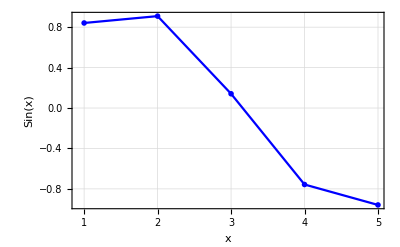

```mathematica
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}
]
```

## Ajuste

```mathematica
VandermondeMatrix[xList_]:=Quiet[Table[x^j /.Indeterminate->1,{x,xList},{j,0,Length[xList]-1}]];
PolynomialBase[n_]:=Table[x^j,{j,0,n-1}];
```

```mathematica
MatrixForm@VandermondeMatrix[datos[[All,1]]]
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16
1 | 3 | 9 | 27 | 81
1 | 4 | 16 | 64 | 256
1 | 5 | 25 | 125 | 625)

```mathematica
aVect= N@Inverse[VandermondeMatrix[datos[[All,1]]]].Transpose[{datos[[All,2]]}]
```

{{-0.649331},{2.36813},{-0.9503},{0.0680069},{0.00497029}}

```mathematica
aList = First@Transpose[aVect]
```

{-0.649331,2.36813,-0.9503,0.0680069,0.00497029}

```mathematica
PolynomialBase[5]
```

{1,x,x^2,x^3,x^4}

```mathematica
aList.PolynomialBase[5]
```

-0.649331+2.36813 x-0.9503 x^2+0.0680069 x^3+0.00497029 x^4

Interpolación

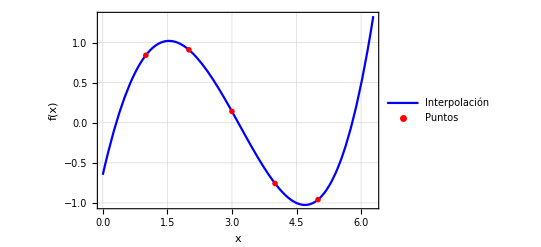

```mathematica
Show[
Plot[
-0.6493310617421598+2.3681253386241767 x-0.9503004509420383 x^2+0.0680068658498752 x^3+0.00497029301803948 x^4,
{x,0,2π},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},PlotLegends->{"Interpolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

Extrapolación

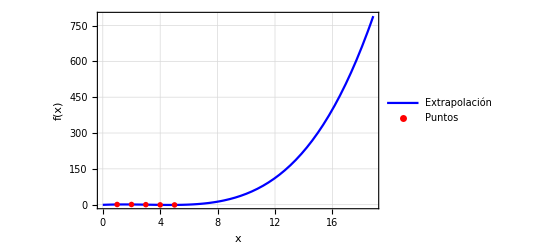

```mathematica
Show[
Plot[
-0.6493310617421598+2.3681253386241767 x-0.9503004509420383 x^2+0.0680068658498752 x^3+0.00497029301803948 x^4,
{x,0,6π},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},PlotLegends->{"Extrapolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

## Análisis del error

```mathematica
R[x_]:=Sin[x]-(-0.6493310617421598+2.3681253386241767 x-0.9503004509420383 x^2+0.0680068658498752 x^3+0.00497029301803948 x^4);
```

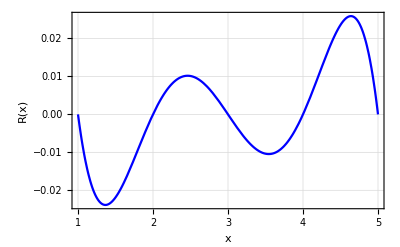

```mathematica
Plot[R[x],{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

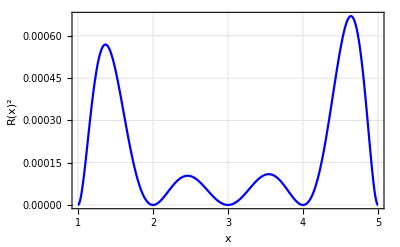

```mathematica
Plot[R[x]^2,{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)^2",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

```mathematica
ϵ = √NIntegrate[R[x]^2,{x,a,b}]
```

0.0266467

## El problema de la interpolación polinomial

```mathematica
a = 1; b = 5;
GenerateData[Δ_]:=Table[{x,Sin[x]},{x,a,b,Δ}];
PolynomialInterpolation[data_]:=Block[{aVect,aList},
aVect= Quiet@N@Inverse[VandermondeMatrix[data[[All,1]]]].Transpose[{data[[All,2]]}];
aList = First@Transpose[aVect];

aList.PolynomialBase[Length[aList]]
];
```

```mathematica
datos = GenerateData[0.5]
```

{{1.,0.841471},{1.5,0.997495},{2.,0.909297},{2.5,0.598472},{3.,0.14112},{3.5,-0.350783},{4.,-0.756802},{4.5,-0.97753},{5.,-0.958924}}

```mathematica
PolynomialInterpolation[datos]
```

-0.0159075+1.06026 x-0.0965252 x^2-0.0809152 x^3-0.0463279 x^4+0.0238785 x^5-0.00309914 x^6+0.0000996397 x^7+3.21959×10^-6 x^8

```mathematica
errorVsData = Block[{data},Table[
data = GenerateData[Δ];
{Length[data],√NIntegrate[(Sin[x]-PolynomialInterpolation[data])^2,{x,a,b}]},
{Δ,0.05,0.5,0.05}
]
];
```

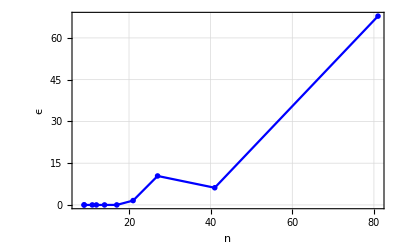

```mathematica
ListLinePlot[errorVsData,
PlotTheme->"Monochrome",FrameLabel->{Style["n",15], Style["ϵ",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```